```mathematica
(* take a fractal set (represented as an ordered list of points between 0 and 1), return the number of filled boxes *)
Clear[bc];
bc[list_,n_,δ_]:=Block[{curLbl=1,curBS=0,Δ,b=δ^-n,nboxes=0,len=Length[list],loop},(*Δ:distance btw the left side of the current box and the current pt*)Δ=list[[curLbl]]-curBS;
While[curLbl≤len,loop=False;
(*while the current pt is in the current box,pass to the pt on its right*)While[Δ≤b&&curLbl<len,curLbl++;Δ=list[[curLbl]]-curBS;
loop=True;];
(*after the loop the current box has jumped of Floor[Δ/b] units,and one more box has points in it*)If[loop,curBS+=b Floor[Δ/b];
nboxes++;Δ=list[[curLbl]]-curBS;,curLbl++;];];
Return[nboxes];]
```

### Example: Hausdorff dimension of the spectrum of the hirarchical chain

```mathematica
(* compute the spectrum *)

(* amplitude de saut entre les sites atomiques i et i+1 *)
Clear[t];
t[i_]:=Block[{k,tt},k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]

(* hamiltonien avec conditions aux bords libres *)
Clear[h];
h[n_]:=Block[{tbl,ar},tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
Normal[ar+Transpose[ar]]]

(* normalized spectrum *)
spect[n_,rr_?NumberQ,vv_?NumberQ]:=Block[{spec,r=rr,v=vv},spec=Sort[Eigenvalues[h[n]]];
spec=(spec-spec[[1]])/(spec[[-1]]-spec[[1]]);
Return[spec];]
```

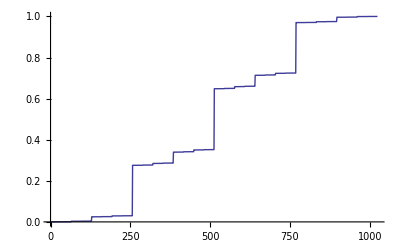

```mathematica
ListPlot[spect[10,.3,1.],Joined->True]
```

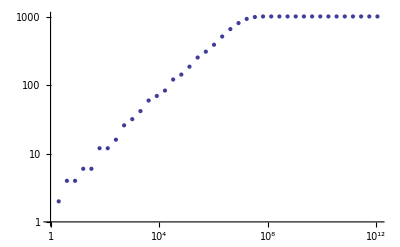

```mathematica
sp=spect[10,.3,.9];
r=Range[1,40,1];
delta=2;
(* compute the number of filled boxes for a whole range of values of n *)
nb=ParallelMap[bc[sp,#,delta]&,r];
(*number of filled boxes as a function of their length*)
dat=Parallelize@MapThread[{#1,#2}&,{delta^r,nb}];
(* the slope is the box-counting dimension of the spectrum *)
ListLogLogPlot[dat]
```

```mathematica
(* now we can fit the slope to get the box-counting dimension *)
xi=10;xf=xi+10;
fit=LinearModelFit[Log10@dat[[xi;;xf]],logl,logl];
Plot[Normal@fit,{logl,0,12},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat}]
```

-Graphics-

#### Complexity

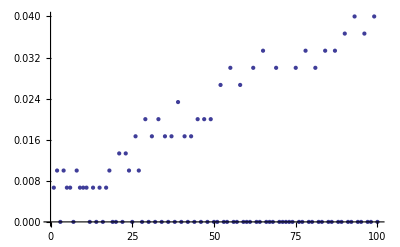

```mathematica
(* bc is at most linear in the number of boxes *)
sp=spect[10,.3,.9];
r=Range[1,100,1];
delta=2;
timebc=Map[Timing[bc[sp,#,delta]][[1]]&,r];
ListPlot[timebc]
```

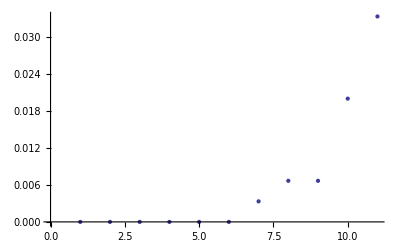

```mathematica
(* bc is exponential in the number of points of the fractal set *)
lsp=ParallelMap[spect[#,.3,.9]&,Range[2,12]];
n=30;
delta=2;
timebc=Map[Timing[bc[#,n,delta]][[1]]&,lsp];
ListPlot[timebc]
```